```mathematica
Manipulate[ParametricPlot[({Sin[n t1],Sin[(n-1) t1]}),{t1,0,2 Pi},Epilog->{Red,PointSize[Large],Table[If[OddQ[i+j],Point[{Cos[Pi i/(2 (n-1))],Cos[Pi j/(2 (n))]}]],{i,2 n-3},{j,2 n-1}]}],{{n,5},2,20,1}]
```

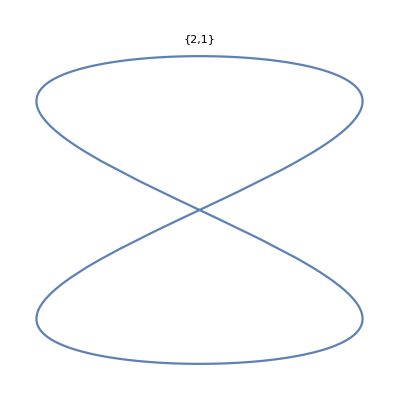
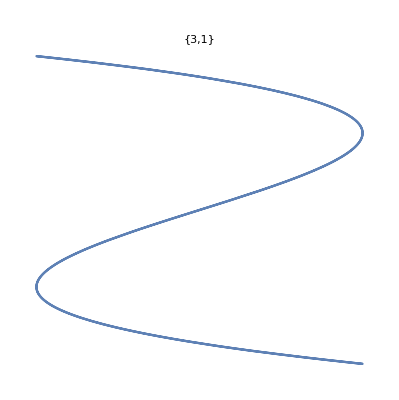
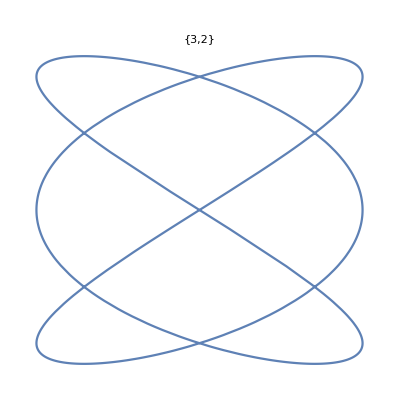
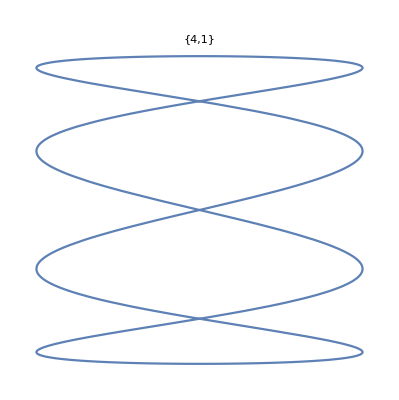
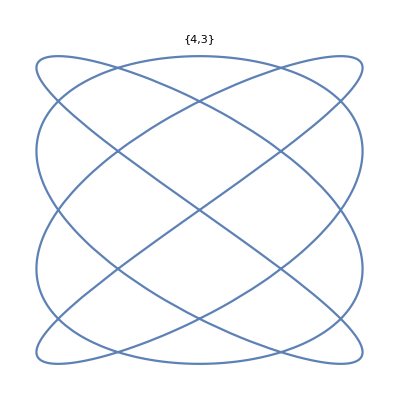
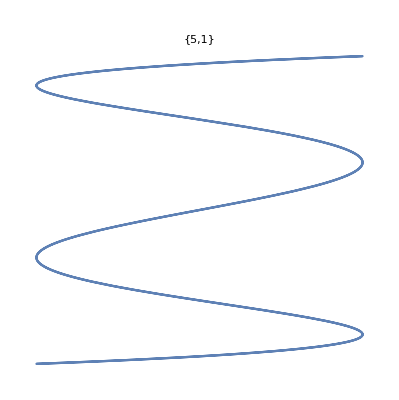
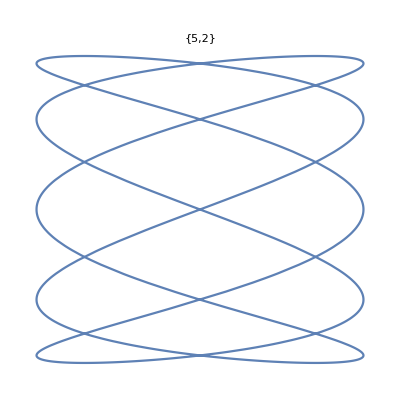
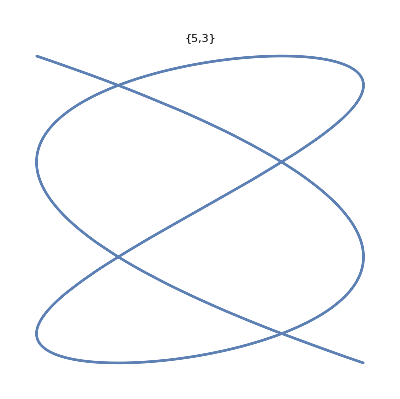

```mathematica
Column[Row/@Table[ParametricPlot[({Sin[a t],Sin[b t]}),{t,0,2 Pi},Epilog->{},PlotLabel->{a,b},Axes->False,ImageSize->Tiny],{a,10},{b,Select[Range[a-1],CoprimeQ[#,a]&]}],Alignment->Center]
```